## Statistical distributions, the copula and credit loss

### Introduction

This major section has nothing to do with credit loss or probabilities of default. Instead, it illustrates statistical definitions that every student should know cold. 

The second major section infers a copula. Not all students have heard about copulas before. Many will hear about them again on their jobs. 

The final section introduces PD, PDJ, and ρ. Then, only then, and not until then. I’ll call attention to the moment that shifts from mathematical statistics to credit loss.

### The joint PDF and CDF of variables X and Y

The following defines a function of x and y in Mathematica. Square brackets indicate arguments of functions.

```mathematica
fxy[x_,y_]:= (1+3 x - y)/2
```

When you see the underscore “_” and the “:=”, this means that a function is being defined in Mathematica. The function “fxy” integrates to 1.0 over the unit square. You can of course check this by hand, and I recommend that. I show two ways to symbolize the integration in Mathematica.

```mathematica
{∫_0^1 ∫_0^1 fxy[x,y]ⅆyⅆx,∫_0^1 ∫_0^1 (1+3 x - y)/2ⅆyⅆx}
```

{1,1}

fxy[ ] takes the value zero when x = 0, y = 1, and it can’t go lower on the unit square.

fxy is nonnegative, and it integrates to 1.0. It could be used as a joint PDF. We assume that it is the  joint PDF of variables x and y. The distribution does not have a name. I propose that we call it the “36702 Distribution.”

The joint CDF of the 36702 distribution is the double integral:

```mathematica
∫∫fxy[x,y]ⅆyⅆx
```

1/4 x (2+3 x-y) y

I define a Mathematica function that produces the joint CDF and plot it on the unit square:

```mathematica
Fxy[x_,y_]:=1/4 x (2+3 x-y) y
```

```mathematica
Plot3D[Fxy[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

A joint CDF is a statement about probabilities. An example would be Prob[ X<.4, Y<.6 ]. Here are two equivalent calculations:

```mathematica
{Fxy[.4,.6],∫_0^(.4) ∫_0^(.6) fxy[x,y]ⅆyⅆx}
```

{0.156,0.156}

### Marginal distributions

To find a marginal PDF in a marginal distribution, integrate out any other variables. I create Mathematica functions, plot them, and spot check their integrals.

```mathematica
Simplify[{∫_0^1 fxy[x,y]ⅆy,∫_0^1 fxy[x,y]ⅆx}]
```

{1/4 (1+6 x),1/4 (5-2 y)}

```mathematica
{fx[x_]:=(1+6x)/4,fy[y_]:=(5-2y)/4};
```

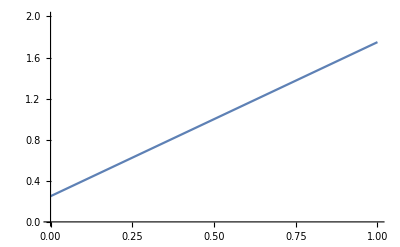
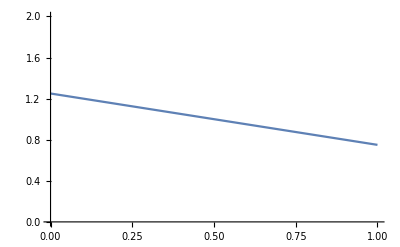

```mathematica
{Plot[fx[x],{x,0,1},PlotRange->{{0,1},{0,2}}],Plot[fy[y],{y,0,1},PlotRange->{{0,1},{0,2}}]}
```

```mathematica
{∫_0^1 fx[x]ⅆx,∫_0^1 fy[y]ⅆy}
```

{1,1}

### Statistical parameter values

Means of X and Y:

```mathematica
{μx=∫_0^1 x fx[x]ⅆx,μy=∫_0^1 y fy[y]ⅆy}
```

{5/8,11/24}

Variances of X and Y:

```mathematica
{σ2x=∫_0^1 (x-5/8)^2 fx[x]ⅆx,σ2y=∫_0^1 (y-11/24)^2 fy[y]ⅆy}
```

{13/192,47/576}

Covariance. This requires the joint distribution of  X and Y:

```mathematica
cov=∫_0^1 ∫_0^1 (x-5/8)(y-11/24)fxy[x,y]ⅆyⅆx
```

1/192

Correlation. The first expression is exact, and the second is the decimal approximation:

```mathematica
{corr=cov/√(σ2x σ2y),corr 1.}
```

{√(3/611),0.0700713}

The correlation of X and Y is 0.070. This is not the ρ that we use. 
Remember, all the credit risk stuff appears later.

If you look at the PDF of a joint normal distribution, you will see an explicit role for means, variances, and correlations. The 36702 distribution and most other distributions do not have this. If you want to know the expected value you must take an expectation, and so forth for variances and correlations.

### CDF and inverse CDF

CDFs of X and Y are integrals of the PDFs:

```mathematica
{∫fx[x]ⅆx,∫fy[y]ⅆy}
```

{1/4 (x+3 x^2),1/4 (5 y-y^2)}

The following also works, and you should review as needed if you are surprised that it does:

```mathematica
{Fxy[x,1],Fxy[1,y]}
```

{1/4 x (1+3 x),1/4 (5-y) y}

```mathematica
{Fx[x_]:=(x+3 x^2)/4,Fy[y_]:=(5y-y^2)/4};
```

CDFs are monotonic, hence, invertible.

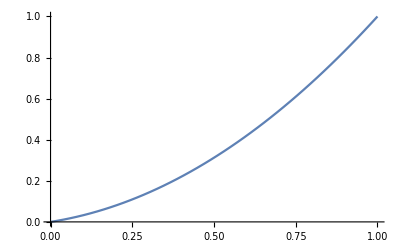
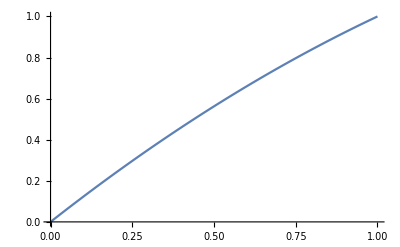

```mathematica
{Plot[Fx[x],{x,0,1}],Plot[Fy[y],{y,0,1}]}
```

I use Mathematica to invert the CDF functions. In Mathematica, the symbol “==” denotes an equation that might be solved. Each equation has two solutions. A solution appears after an arrow.

```mathematica
Solve[q==Fx[x],x]
```

{{x→1/6 (-1-√(1+48 q))},{x→1/6 (-1+√(1+48 q))}}

```mathematica
invFx[q_]:=1/6 (-1+Sqrt[1+48 q])
```

```mathematica
Solve[q==Fy[y],y]
```

{{y→1/2 (5-√(25-16 q))},{y→1/2 (5+√(25-16 q))}}

```mathematica
invFy[q_]:=1/2 (5-Sqrt[25-16 q])
```

Inverse CDFs are monotonic:

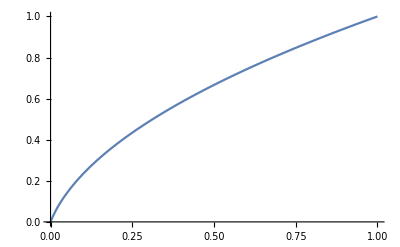
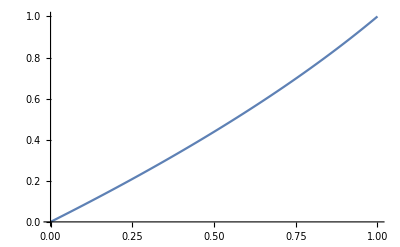

```mathematica
{Plot[invFx[q],{q,0,1}],Plot[invFy[q],{q,0,1}]}
```

### Example

Take a sample of 100,000 values from a Uniform distribution. The sample is uniformly distributed:

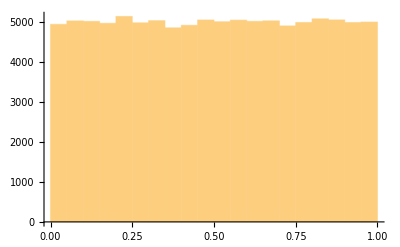

```mathematica
sampleOfUniform=RandomVariate[UniformDistribution[{0,1}],100000];Histogram[sampleOfUniform]
```

If you apply invFx to each of the values, the 100,000 transformed values obey the distribution of X. Take the average. It is as we calculated earlier:

```mathematica
{Mean[invFx[sampleOfUniform]],μx}
```

{0.625227,5/8}

### Commentary

Starting with a joint distribution of two variables, we inferred the two marginal distributions.

We cannot go the other way. Given only two marginal distributions by themselves, we do not know how they should be related to each other.

We might assume the variables are independent. Then the joint PDF equals the product of the two marginal PDFs.

But independent variables are hard to come by in Financial Math. We want to relate the variables to each other in some other way, and there is a vast and trackless land of copulas that might be used.

Now we return to the main task of this exercise.

## The copula

### The plan for finding the copula

Summarizing the previous major section, we have a pair of variables, {X, Y}, that obey the 36702 distribution. We found the PDFs and CDFs of X and of Y and found the inverse CDFs. Hidden somewhere within the joint distribution is the 36702 copula that connects the two marginal distributions. We wish to infer the copula from the distribution. We find that we can write the 36702 copula in compact form. It is very different from the 36702 distribution. 

Lecture 1 Slide 59 tells, “The copula is defined as a multivariate distribution where every marginal distribution is the uniform distribution.” So every copula is a multivariate distribution, and the variables being described have uniform distributions. You could call a copula the connection between the variables in raw form. Once you have some uniform distributions connected in the desired way, you can convert each to a distribution that you like better.

The conversion depends again on the probability integral transform. If X is a random variable and you symbolize its CDF as F [ ], then the random variable F[X] has the uniform distribution. If U is a random number and has the uniform distribution, then the random number F^-1[U] has the CDF F[ ]. Note that the symbol F^-1 denotes the functional  inverse, not the numerical inverse.

Returning to point, Fxy is a multivariate distribution of variables. It is not, itself, the copula because the marginal distributions are not uniform. We need to:
	1. Convert X to the quantile of X and convert Y to the 		     quantile of Y.
	2. Give the quantiles to some function.
	3. If the function always produces the same value as Fxy, 	     then the function is the 36702 copula. 

1. The variables Fx[X] and Fy[Y] have uniform distributions. The value Fx[x] is the quantile of x and the value F[y] is the quantile of y.

2. What kind of function would map the quantiles of X and Y to the value of Fxy? How about a function that converts the quantile of X to the value of X,  converts the quantile of Y to the value of Y, and gives those values of X and Y to the function Fxy? 

3. The function being described in point 2 is guaranteed to produce the value of Fxy. It is a joint CDF that connects uniform variables. It is the copula.

### Finding the copula

Here is function that takes X and Y as inputs and produces the value of Fxy:

	Fxy[ x, y ] = Fxy[  invFx[ Fx[ x ]], invFy[ Fy[ y ]]   ] 

I introduce symbols xu = Fx[ x ] and yu = Fy[ y ]. Making this substitution, I create a new function:
	C36702[ xu, yu ] = Fxy[ invFx[ xu ], invFy[ yu ]  ].
Bingo! That’s the 36702 copula. Its arguments are the quantile of X and the quantile of Y, and its value is the the joint CDF of the 36702 cumulative distribution evaluated at those quantiles. I ask Mathematica to simplify:

```mathematica
Simplify[Fxy[invFx[xu],invFy[yu]]]
```

-1/96 (-1+√(1+48 xu)) (-5+√(25-16 yu)) (-2+√(1+48 xu)+√(25-16 yu))

As is often the case, the copula does not impart a deep pool of understanding. Even to see that it is nonnegative takes some looking. I create a function for the copula and graph it:

```mathematica
C36702[xu_,yu_]:=-(1/96) (-1+Sqrt[1+48 xu]) (-5+Sqrt[25-16 yu]) (-2+Sqrt[1+48 xu]+Sqrt[25-16 yu])
```

```mathematica
Plot3D[C36702[xu,yu],{xu,0,1},{yu,0,1}]
```

-Graphics3D-

### Spot check

Let’s see whether Fxy and C36702 give the same answer for a pair of values of {X, Y}. Let’s use their median values. The copula gives the probability that each variable is less than its median, Prob [ xu < .5,  yu < .5 ]:

```mathematica
C36702[.5,.5]
```

0.260259

To check whether Fxy gives the same value, we need the median values of the variables, X and Y:

```mathematica
{invFx[.5],invFy[.5]}
```

{0.666667,0.438447}

The joint distribution agrees:

```mathematica
Fxy[.666667,.438447]
```

0.260259

So that’s a match. If you wanted the PDF instead...

### A disappointing discovery

I hope that this exercise distinguishes some slippery ideas.

In practice, I’ve never discovered or been given a joint distribution. Instead, I find some univariate distributions and wonder how to connect them. There are surprisingly few candidates for a general-purpose copula of three or more variables;  the answer tends to be the Gauss copula or the t-copula. The differences between the two are the degree of tail dependence, the degree of familiarity, and the ease of use. I haven’t been in  situations where I had enough data to do a workmanlike statistical test to see what the data want. Stock risk models sometimes use the t-4 copula. I doubt that t-4 is statistically distinguishable from the t-3 or t-5.

Paul Embrechts, the author of the excellent book Quantitative Risk Management, says that copulas have only three uses: pedagogy, pedagogy, and stress testing. It is hilarious when he says it, if you have studied the book.

## Portfolio credit loss

### Plan

I would like to call attention to this moment because we now start talking about credit loss.

Lecture 1 introduces the idea of a latent variable responsible for the default of a firm. Slide 40 says that you could use just about any random variable. If the quantile of the latent variable is less than PD, then count that as a default.

We have two firms. We use the 36702 distribution to model the defaults of them.

### Question

Suppose that PD_x=0.1, PD_Y=0.2, and the latent variables X and Y responsible for default obey the  36702 distribution:  
	f_(x,y)[ x, y ]= ( 1 + 3 x - y ) / 2.
What are the values of PDJ, Dcorr, and ρ?